```mathematica
ClearAll[filterTable,path,data,table,table0,table1,table2,A,α,β,B,iB,Z,V,v,years,hist,theory,isoquant]
```

Вспомогательная функция, чтобы убрать шапку таблицы и пустые строки

```mathematica
filterTable[table_List] := 
Module[{newTable = table, n = Length@table},
Select[newTable, NumberQ[#⟦1⟧]&]];
```

Указываем путь к данным и импортируем их

```mathematica
SetDirectory[NotebookDirectory[]];
path = "data1.xls";
```

```mathematica
data = Import[path]⟦1⟧;
```

Проводим первичную обработку данных. Таблицу транспонируем для удобства вычислений

```mathematica
table = Transpose@filterTable[data];
```

```mathematica
table //Transpose//TableForm
```

1936. | 83278. | 234236. | 73426.
1937. | 90884. | 254890. | 77568.
1938. | 83743. | 217606. | 70460.
1939. | 91530. | 221746. | 75131.
1940. | 101313. | 228757. | 79694.
1941. | 116415. | 250238. | 89276.
1942. | 127434. | 266469. | 97056.
1943. | 136274. | 266154. | 101633.
1944. | 146470. | 269520. | 100124.
1945. | 145052. | 263098. | 94920.
1946. | 140288. | 252357. | 96671.
1947. | 142022. | 262536. | 100072.
1948. | 149895. | 285700. | 101304.
1949. | 147122. | 277522. | 96784.
1950. | 163620. | 307946. | 100352.

Убираем строку/столбец с годом

```mathematica
table0 = table⟦{2,3,4}⟧;
```

```mathematica
table0 //Transpose//TableForm
```

83278. | 234236. | 73426.
90884. | 254890. | 77568.
83743. | 217606. | 70460.
91530. | 221746. | 75131.
101313. | 228757. | 79694.
116415. | 250238. | 89276.
127434. | 266469. | 97056.
136274. | 266154. | 101633.
146470. | 269520. | 100124.
145052. | 263098. | 94920.
140288. | 252357. | 96671.
142022. | 262536. | 100072.
149895. | 285700. | 101304.
147122. | 277522. | 96784.
163620. | 307946. | 100352.

Вспомогательная таблица со строками/столбцами lnY, lnK, lnL

```mathematica
table1 = Log@table0;
```

```mathematica
table1//Transpose//TableForm
```

11.3299 | 12.3641 | 11.204
11.4173 | 12.4486 | 11.2589
11.3355 | 12.2904 | 11.1628
11.4244 | 12.3093 | 11.227
11.526 | 12.3404 | 11.2859
11.6649 | 12.4302 | 11.3995
11.7554 | 12.493 | 11.483
11.8224 | 12.4918 | 11.5291
11.8946 | 12.5044 | 11.5142
11.8848 | 12.4803 | 11.4608
11.8515 | 12.4386 | 11.4791
11.8637 | 12.4781 | 11.5136
11.9177 | 12.5627 | 11.5259
11.899 | 12.5337 | 11.4802
12.0053 | 12.6377 | 11.5164

Вспомогательная таблица со строками/столбцами ln^2K, ln^2L, lnK*lnL, lnY*lnK, lnY*lnL

```mathematica
table2 = {(table1⟦2⟧)^2,(table1⟦3⟧)^2,table1⟦2⟧*table1⟦3⟧,table1⟦1⟧*table1⟦2⟧,table1⟦1⟧*table1⟦3⟧};
```

```mathematica
table2//Transpose //TableForm
```

152.871 | 125.53 | 138.528 | 140.084 | 126.941
154.967 | 126.763 | 140.158 | 142.13 | 128.547
151.055 | 124.608 | 137.196 | 139.318 | 126.536
151.519 | 126.045 | 138.196 | 140.626 | 128.262
152.286 | 127.373 | 139.273 | 142.235 | 130.082
154.509 | 129.948 | 141.698 | 144.997 | 132.974
156.075 | 131.86 | 143.458 | 146.86 | 134.987
156.046 | 132.921 | 144.02 | 147.684 | 136.302
156.36 | 132.576 | 143.978 | 148.735 | 136.956
155.757 | 131.35 | 143.034 | 148.326 | 136.21
154.719 | 131.769 | 142.784 | 147.415 | 136.044
155.704 | 132.564 | 143.669 | 148.037 | 136.595
157.821 | 132.846 | 144.796 | 149.718 | 137.362
157.093 | 131.796 | 143.889 | 149.138 | 136.604
159.711 | 132.628 | 145.541 | 151.719 | 138.258

Составляем матрицу коэффициентов В

```mathematica
B = ({{Length@First@table2, Total@table1⟦2⟧, Total@table1⟦3⟧}, {Total@table1⟦2⟧, Total@table2⟦1⟧, Total@table2⟦3⟧}, {Total@table1⟦3⟧, Total@table2⟦3⟧, Total@table2⟦2⟧}});
```

```mathematica
B//MatrixForm
```

(15 | 186.803 | 171.041
186.803 | 2326.49 | 2130.22
171.041 | 2130.22 | 1950.58)

Находим обратную матрицу В

```mathematica
iB = Inverse@B;
```

```mathematica
iB//MatrixForm
```

(1391.73 | -158.908 | 51.5052
-158.908 | 28.788 | -17.5051
51.5052 | -17.5051 | 14.6013)

Составляем вектор-столбец правых частей

```mathematica
Z = ({{Total@table1⟦1⟧}, {Total@table2⟦4⟧}, {Total@table2⟦5⟧}});
```

```mathematica
Z//MatrixForm
```

(175.592
2187.02
2002.66)

Получаем искомый вектор, умножая обратную матрицу на вектор правых частей

```mathematica
V= iB.Z;
```

```mathematica
V //MatrixForm
```

(-9.65104
0.358166
1.48182)

Первый элемент столбца -- lnA. Заменяем его на значение коэффициента A

```mathematica
v = ReplacePart[V, 1->Exp[V⟦1⟧]];
```

```mathematica
v//MatrixForm
```

(0.0000643589
0.358166
1.48182)

Получаем искомые параметры

```mathematica
A = v⟦1,1⟧;
α = v⟦2,1⟧;
β = v⟦3,1⟧;
```

Строим графики

```mathematica
years = IntegerPart@table⟦1⟧;
```

```mathematica
hist = table⟦2⟧
```

{83278.,90884.,83743.,91530.,101313.,116415.,127434.,136274.,146470.,145052.,140288.,142022.,149895.,147122.,163620.}

```mathematica
theory = A*(table⟦3⟧)^α*(table⟦4⟧)^β;
```

```mathematica
ListLinePlot[{Transpose[{years,hist}],Transpose[{years,theory}]},PlotLabels->{"hist","theory"},AxesLabel->{"year","GDP"}]
```

-Graphics-

Строим изокванту (ВВП = 100 000)

```mathematica
isoquant = Table[{k,(100000/(A*k^α))^(1/β)},{k,100000,400000,10000}];
```

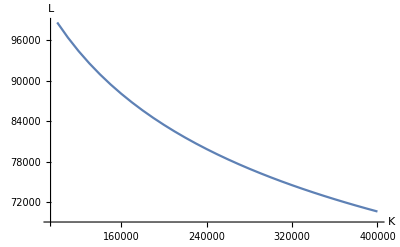

```mathematica
ListLinePlot[isoquant,AxesLabel->{"K","L"}]
```